# Lista I - Física Matemática 1

Lyliana Myllena Santos de Sousa - 11223740
Lyliana.Sousa@usp.br

## 1.a)

Mostraremos que a soma das funções periódicas 𝒻_1 e 𝒻_2 de períodos L_1 e L_2 é uma função periódica de período mL_1, onde mL_1=nL_2, a partir dos três propriedades das funções periódicas a seguir:
 →  𝒻( x + T) = 𝒻(x), sendo T = nL, onde T é o período multiplicado por um número inteiro.
 →  Sendo 𝒻_1 e 𝒻_2 duas funções periódicas de mesmo período, temos que:
  𝒻_1( x + L) + 𝒻_2( x + L) = [ 𝒻_1 + 𝒻_2]( x + L)  =  [ 𝒻_1 + 𝒻_2]( x ) =  𝒻_1( x ) + 𝒻_2( x )
  → Com o item acima, podemos observar que a soma de funções periódicas com um mesmo múltiplo de período, nos dará uma função periódica de período igual ao múltiplo de período. Ou seja,
  𝒻_1( x + L_1) + 𝒻_2( x + L_2) =  𝒻_1( x + mL_1) + 𝒻_2( x + nL_2) = 𝒻_1( x + T) + 𝒻_2( x + T) =[ 𝒻_1 + 𝒻_2]( x +T)  =
  [ 𝒻_1 + 𝒻_2]( x ) , sendo T = mL_1 o período da função soma.

## 1.b)

Sendo 𝒻(x) uma função periódica de período L, ela pode ser escrita como uma série de Fourier Complexa.
 𝒻(x) = ∑_(n ∈ ℤ) c_n ℯ^(ⅈ2πnx/L) (1.1), supondo que a nossa função converge. Integraremos ela de 0 à L.
 ∫_0^L 𝒻(x)ⅆx =  ∑_(n ∈ ℤ) c_n∫_0^L ℯ^(ⅈ2πnx/L)ⅆx = ∑_(n ∈ ℤ) c_n ⅈ2πn/L∫_0^ⅈ2πn ℯ^u ⅆu = ∑_(n ∈ ℤ) c_n ⅈ2πn/L ℯ^u|_0^ⅈ2πn = ∑_(n ∈ ℤ) c_n ⅈ2πn/L[ℯ^ⅈ2πn- 1] ⟺  ∫_0^L 𝒻(x)ⅆx = 0 (1.2)
 Lembrando que 𝒶_0= 2/L∫_0^L 𝒻(x)ⅆx (1.3), temos então que 𝒶_0 = 0.  Sendo c_n=1/2(𝒶_n- ⅈ𝒷_n) (1.4), e lembrando que 𝒷_0 é sempre 0, temos que  c_0= 1/2 𝒶_0= 0. Com isso, temos que c_0 e 𝒶_0, que são os nossos coeficientes de Fourier são zeros. Disso eu tiro que a área de 𝒻(x) é nula quando seu coeficiente linear é nulo, ou vice versa.
 Se somarmos uma constante a uma função linear, ela continuará sendo uma função linear, só estará translada, porém se integrarmos essa função translada no período, teremos que:
 𝒻^-(x) = 𝒻(x) + cte;  ∫_0^L 𝒻^-(x)ⅆx  = ∫_0^L 𝒻(x)ⅆx  +∫_0^L cteⅆx = cte*L, ou seja essa função não será mais periódica.

## 1.c)

Sendo 𝒻 e ℊ  duas funções periódicas de mesmo período. Podemos escrever ambas funções como uma série de Fourier da forma complexa, com isso temos:
 𝒻(x-y) = ∑_(n ∈ ℤ) c_n ℯ^(ⅈ2πn/L(x-y)) (2.1) e  ℊ(x) = ∑_(n ∈ ℤ) c_n^-ℯ^(ⅈ2πny/L) (2.2)
 A partir das relações a cima, obteremos a convolução das funções:
 𝒻(x-y)ℊ(x) =  ∑_(n ∈ ℤ) c_n ℯ^(ⅈ2πn/L(x-y))∑_(n ∈ ℤ) c_n^-ℯ^(ⅈ2πny/L) = ∑_(n ∈ ℤ) c_n c_n^-ℯ^(ⅈ2πnx/L) (2.3), lembrando que c_n e c_n^- é um valor que só depende de n.
 ∫_0^L 𝒻(x-y)ℊ(x)ⅆy =  ∑_(n ∈ ℤ) c_n c_n^-ℯ^(ⅈ2πnx/L)∫_0^L ⅆy = ∑_(n ∈ ℤ) c_n c_n^-ℯ^(ⅈ2πnx/L)L (2.4)
 1/L∫_0^L 𝒻(x-y)ℊ(x)ⅆy = ∑_(n ∈ ℤ) c_n c_n^-ℯ^(ⅈ2πnx/L)(2.5)
 Ao final, observamos que a convolução possui uma formato de série de Fourier, sendo assim periódica no período L.

## 2.a)

Calcularemos a série de Fourier de 𝒻(x)= Cos(αx) para ser periódica por partes em [-π,π] , com um período L =2π, para α um número real, no final dessa célula podemos observar alguns exemplos dessas funções de plot  𝒻(x) para diferentes tipos de α.
		𝒻(x)= 𝒶_0/2+∑_(n=1)^∞ {𝒶_n Cos((2π n)/L x) + 𝒷_n Sin((2π n)/L x)}  (2.1), sendo os seus coeficientes:
	𝒶_0= 2/L∫_0^L 𝒻(x)ⅆx (2.2) ;	𝒶_n= 2/L∫_0^L 𝒻(x)Cos((2π n)/L x)ⅆx (2.3);	𝒷_n= 2/L∫_0^L 𝒻(x)Sin((2π n)/L x)ⅆx (2.4);
Considerando que L = 2π e sendo o nosso intervalo [-π,π], temos:		
		𝒻(x)= 𝒶_0/2+∑_(n=1)^∞ {𝒶_n Cos(nx) + 𝒷_n Sin(nx)} (2.5)
		𝒶_0= 1/π∫_-π^π 𝒻(x)ⅆx ;	𝒶_n= 1/π∫_-π^π 𝒻(x)Cos(nx)ⅆx;	𝒷_n= 1/π∫_-π^π 𝒻(x)Sin(nx)ⅆx;	
Começarei calculando o 𝒶_0:
𝒶_0= 1/π∫_-π^π 𝒻(x)ⅆx = 1/π∫_-π^π Cos(x)ⅆx = 1/απ[Sin(απ)-Sin(-απ)]	⟹	𝒶_0 =  2/απ Sin(απ) (2.6)

	Antes de calcularmos {𝒶_n, 𝒷_n} devemos observar a paridade da função 𝒻(x). Cos(αx) é uma função par, então sua série de Fourier deve ser formada por uma somatória se funções pares (uma série de cossenos), com isso já conseguimos observar de imediato que 𝒷_n=0 (2.7)
Calculando 𝒶_n:
𝒶_n= 1/π∫_-π^π 𝒻(x)Cos(nx)𝕕x=1/π∫_-π^π Cos(αx)Cos(nx)ⅆx
Pela propriedade trigonométrica, a seguir : Cos(αx)Cos(nx) = 1/2[Cos(αx + nx) + Cos(αx - nx)]
𝒶_n=1/(2π)∫_-π^π Cos([α-n]x)ⅆx + 1/(2π)∫_-π^π Cos([α+n]x)ⅆx, fazendo um substituição, temos:
𝒶_n=1/(2π)[1/[α-n]∫_(-π[α-n])^π[α-n] Cos(u)ⅆu + 1/[α+n]∫_(-π[α+n])^π[α+n] Cos(t)ⅆt]
𝒶_n=1/(2π)[2/[α-n]Sin(π[α-n]) + 2/[α+n]Sin(π[α+n])] =1/π[1/[α-n]Sin(π[α-n]) + 1/[α+n]Sin(π[α+n])] (2.8)
	Para simplificar o 𝒶_n utilizaremos as seguintes considerações:
- Sendo n um numero inteiro, então: Sin(nπ)= 0 e Cos(nπ)= (-1)^n
- Pela propriedade trigonométrica Sin(A + B) = Sin(A)Cos(B) + Cos(A)Sin(B), teremos que: Sin(π[α-n])=Sin(π[α+n])= Sin(απ)(-1)^n
𝒶_n=1/π[1/[α-n]Sin(π[α-n]) + 1/[α+n]Sin(π[α+n])]=1/π[(2αSin(απ)(-1)^n)/(α^2-n^2)] =(Sin(απ))/π[(2(α(-1))^n)/(α^2-n^2)] ⟹ 	𝒶_n=(Sin(απ))/π[(2(α(-1))^n)/(α^2-n^2)] (2.9)
Observação: Para entendermos o que acontece quando α = n ou α = -n, usaremos um dos limites fundamentais do calculo: Limit[(Sin(ωx))/x,ωx→0]=ω na Eq.(2.8) com isso chegaremos que 𝒶_n= 1/π[π + (Sin(2πα))/(2α)] (2.10)
	Com isso teremos a série de Fourier para α ∈ ℝ:
𝒻(x) = (Sin(απ))/απ + ∑_(n=1)^∞ (Sin(απ))/π[(2(α(-1))^n)/(α^2-n^2)]Cos(nx)= (Sin(απ))/π [1/α+ ∑_(n=1)^∞ [(2(α(-1))^n)/(α^2-n^2)]Cos(nx)] (2.11)
	Agora analisaremos  nossa série de Fourier para α ∈ ℤ:
- Começarei com α = 0. Para α = 0 observamos pelo limite fundamental que 𝒶_0= 2 e 𝒶_n=𝒷_n= 0. Com isso 𝒻(x)= 1, o que faz sentindo já que Cos(0) = 1.
- Para α ∈ ℤ^*, devemos lembrar que para n ∈ ℤ ⇔ Sin(nx)=0. Com isso 𝒶_0=𝒷_n= 0. Agora devemos analisar o 𝒶_n para α = n e α ≠ n:
	→Para  α = n, temos a Eq.  (2.10) sendo que o Sin(2πα) = 0, com isso 𝒶_n=1.
	→Para α ≠ n, temos que 𝒶_n=(Sin(απ))/π[(2(α(-1))^n)/(α^2-n^2)] = 0 
Com as informações acima temos que a somatória dos cossenos será diferente de zero apenas quando α = n. Com isso
𝒻(x) = 0 + ∑_(n=1)^∞ (Sin(απ))/π[(2(α(-1))^n)/(α^2-n^2)]Cos(nx)= Cos(αx)

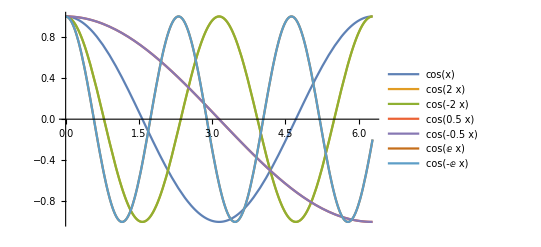

```mathematica
(*Observaremos abaixo alguns exemplos de plots para diferentes valores de α*)
Plot[{Cos[x],Cos[2x],Cos[-2x], Cos[0.5*x],  Cos[-0.5*x],  Cos[ⅇ*x],  Cos[-ⅇ*x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

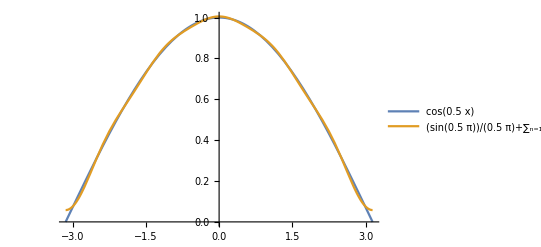

```mathematica
Plot[{Cos[0.5 x], Sin[0.5 π]/(0.5 π)+ Sum[(-1)^n/π*(2 *0.5)/(0.5^2-n^2)*Sin[0.5 π]*Cos[n x], {n, 1, 5}]}, {x, -π,π}, PlotLegends->"Expressions"]
```

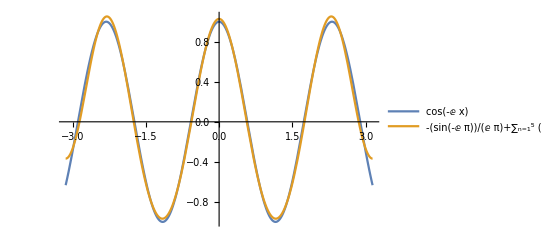

```mathematica
Plot[{Cos[-ⅇ x], Sin[-ⅇ π]/(-ⅇ π)+ Sum[(-1)^n/π*(-2 ⅇ)/(ⅇ^2-n^2)*Sin[-ⅇ π]*Cos[n x], {n, 1, 5}]}, {x, -π,π}, PlotLegends->"Expressions"]
```

## 2.b)

A relação trigonométrica Cot(x)=(Cos(x))/(Sin(x)). A Eq.(2.11) para x = π, nos dará:
𝒻(x) =  (Sin(απ))/π [1/α+ ∑_(n=1)^∞ [(2(α(-1))^n)/(α^2-n^2)]Cos(nx)]	⟹	 Cos(απ) = (Sin(απ))/π [1/α+ ∑_(n=1)^∞ [(2(α(-1))^n)/(α^2-n^2)]Cos(π n)] 	⟹	Cos(απ) = (Sin(απ))/π [1/α+ ∑_(n=1)^∞ [(2(α(-1))^n)/(α^2-n^2)](-1)^n]	⟹	Cos(απ) = (Sin(απ))/π [1/α+ ∑_(n=1)^∞ [(2(α(-1))^(2n))/(α^2-n^2)]]	⟹	(Cos(απ))/(Sin(απ)) = 1/π [1/α+ ∑_(n=1)^∞ [(2α)/(α^2-n^2)]]
Cot(αx) =1/π [1/α+ ∑_(n=1)^∞ [(2α)/(α^2-n^2)]]

## 3.a)

Sendo  𝒻(x) uma função periódica com período L. Teremos que a sua série e coeficiente de Fourier terão o seguinte formato:
		𝒻(x)= 𝒶_0/2+∑_(n=1)^∞ {𝒶_n Cos((2π n)/L x) + 𝒷_n Sin((2π n)/L x)}  (3.1), sendo os seus coeficientes:
	𝒶_0= 2/L∫_0^L 𝒻(x)ⅆx (3.2) ;	𝒶_n= 2/L∫_0^L 𝒻(x)Cos((2π n)/L x)ⅆx (3.3);	𝒷_n= 2/L∫_0^L 𝒻(x)Sin((2π n)/L x)ⅆx (3.4);
	Sendo ℊ(x) = 𝒻(x +α), com α ∈ ℝ , sua serie e coeficiente de fourier serão: 
		ℊ(x)= 𝒶_0^-/2+∑_(n=1)^∞ {𝒶_n^-Cos((2π n)/L x) + 𝒷_n^-Sin((2π n)/L x)}  (3.5), sendo os seus coeficientes:
	𝒶_0^-= 2/L∫_0^L ℊ(x)ⅆx (3.6) ;	𝒶_n^-= 2/L∫_0^L ℊ(x)Cos((2π n)/L x)ⅆx (3.7);	𝒷_n^-= 2/L∫_0^L ℊ(x)Sin((2π n)/L x)ⅆx (3.8);
	Agora encontrarei os coeficientes de Fourier da ℊ(x) em função dos coeficientes de 𝒻(x);
→ Para encontrarmos o 𝒶_0, primeiro trocaremos a função ℊ(x) por uma relação de 𝒻(x), depois faremos uma mudança de variável na integral (y = x + α  ⇒ dy = dx). Isso mudará os nossos limites de integração, no entanto, como ℊ(x) é uma função periódica (ela é a função 𝒻(x) com uma “fase”), podemos transladar o seu intervalo de integração.
𝒶_0^-= 2/L∫_0^L ℊ(x)ⅆx = 2/L∫_0^L 𝒻(x+α)ⅆx = 2/L∫_α^(L+α) ℊ(y)ⅆy =  2/L∫_0^L ℊ(y)ⅆy = 𝒶_0 
Portanto 𝒶_0^- = 𝒶_0 (3.9)
→ Para encontrarmos o 𝒶_n , seguiremos o mesmo passo do 𝒶_0 até chegarmos na mudança de variável. Neste ponto usaremos a relação trigonométrica a seguir:
 Cos((2π n)/L y -(2π n)/L α)=Cos((2π n)/L y )Cos((2π n)/L α)+Sin((2π n)/L y )Sin((2π n)/L α) (3.10)
 Após mudarmos a relação trigonométrica, tiraremos  as constantes da integral e, como já foi citado anteriormente, transladaremos o intervalo de integração.
𝒶_n^-= 2/L∫_0^L ℊ(x)Cos((2π n)/L x)ⅆx =  2/L∫_0^L 𝒻(x+α)Cos((2π n)/L x)ⅆx =  2/L∫_α^(L+α) 𝒻(y)Cos((2π n)/L(y - α))ⅆy = 2/L Cos((2π n)/L α)∫_α^(L+α) 𝒻(y)Cos((2π n)/L y) ⅆy +2/L Sin((2π n)/L α)∫_α^(L+α) 𝒻(y)Sin((2π n)/L y) ⅆy = 2/L Cos((2π n)/L α)∫_0^L 𝒻(y)Cos((2π n)/L y) ⅆy +2/L Sin((2π n)/L α)∫_0^L 𝒻(y)Sin((2π n)/L y) ⅆy 
Portanto,  𝒶_n^-= 𝒶_n Cos((2π n)/L α) +𝒷_n Sin((2π n)/L α) (3.11)
→ Para encontrarmos o  𝒷_n, seguiremos os mesmo passos do 𝒶_n, com uma diferença apenas na relação trigonométrica que usaremos, que será:
 Sin((2π n)/L y -(2π n)/L α)=Sin((2π n)/L y )Cos((2π n)/L α)-Cos((2π n)/L y )Sin((2π n)/L α) (3.12)
 𝒷_n^-= 2/L∫_0^L ℊ(x)Sin((2π n)/L x)ⅆx = 2/L∫_0^L 𝒻(x+α)Sin((2π n)/L x)ⅆx = 2/L∫_α^(L+α) 𝒻(y)Sin((2π n)/L(y - α))ⅆy = 2/L∫_α^(L+α) 𝒻(y)[Sin((2π n)/L y )Cos((2π n)/L α)-Cos((2π n)/L y )Sin((2π n)/L α) ]ⅆy = 
 2/L Cos((2π n)/L α)∫_α^(L+α) 𝒻(y)Sin((2π n)/L y )-2/L Sin((2π n)/L α)∫_α^(L+α) 𝒻(y)Cos((2π n)/L y )]ⅆy =  2/L Cos((2π n)/L α)∫_0^L 𝒻(y)Sin((2π n)/L y )-2/L Sin((2π n)/L α)∫_0^L 𝒻(y)Cos((2π n)/L y )]ⅆy
 Portanto,  𝒷_n^-=  Cos((2π n)/L α)𝒷_n-Sin((2π n)/L α)𝒶_n(3.13)
 Com isso, terei que serie de Fourier de ℊ(x) = 𝒻(x +α):
 	
ℊ(x)=𝒶_0/2+ ∑_(n=1)^∞ {[ 𝒶_n Cos((2π n)/L α) +𝒷_n Sin((2π n)/L α)]Cos((2π n)/L x) + [Cos((2π n)/L α)𝒷_n-Sin((2π n)/L α)𝒶_n]Sin((2π n)/L x)} (3.14)

## 3.b)

Agora realizaremos um processo semelhante ao do item 3.a), onde ℊ(x)= 𝒻(x) + β. 
ℊ(x)= 𝒶_0^-/2+∑_(n=1)^∞ {𝒶_n^-Cos((2π n)/L x) + 𝒷_n^-Sin((2π n)/L x)} 
→ Para encontrarmos o 𝒶_0, foi bem simples, apenas realizemos usei a propriedade distributiva e fiz uma substituição. 
𝒶_0^-= 2/L∫_0^L ℊ(x)ⅆx = 2/L∫_0^L (𝒻(x)+ β)ⅆx =  2/L∫_0^L 𝒻(x)ⅆx +  2/L∫_0^L βⅆx 
Portanto,  𝒶_0^-= 𝒶_0+2β (3.15)
→ Para encontrarmos o 𝒶_n faremos o mesmo processo para encontrarmos 𝒶_0, até chegarmos na integral ∫_0^L βCos((2π n)/L x)ⅆx, onde o seu resultado será β/(π n)Sin(2π n), que conforme  vimos no exercício 2, será zero.
𝒶_n^-= 2/L∫_0^L ℊ(x)Cos((2π n)/L x)ⅆx =  2/L∫_0^L (𝒻(x)+ β)Cos((2π n)/L x)ⅆx = 2/L∫_0^L 𝒻(x)Cos((2π n)/L x)ⅆx + 2/L∫_0^L βCos((2π n)/L x)ⅆx = 𝒶_n + 2/L βL/(2π n)Sin(2π n) 
Portanto,  𝒶_n^-= 𝒶_n (3.16)
→ Para encontrarmos o 𝒷_nfaremos o mesmo processo para encontrarmos 𝒶_n, com a diferença que a integral ∫_0^L βSin((2π n)/L x)ⅆx será  β/(π n)[Cos(2π n) - 1] = 0, já que Cos(2π n)=1.
𝒷_n^-= 2/L∫_0^L ℊ(x)Sin((2π n)/L x)ⅆx =  2/L∫_0^L (𝒻(x)+ β)Sin((2π n)/L x)ⅆx = 2/L∫_0^L 𝒻(x)Sin((2π n)/L x)ⅆx + 2/L∫_0^L βSin((2π n)/L x)ⅆx = 𝒷_n - 2/L βL/(2π n)[Cos(2π n) - 1] 
Portanto,  𝒷_n^-= 𝒷_n (3.17)

## 4.

Utilizaremos a formulação complexa para calcular a série de Fourier 𝒻(x)= ℯ^λx definida como periódica por partes no intervalo [-π,π], ou seja, tem período L= 2π. Abaixo podemos observar o gráfico para diferentes tipos de λ.

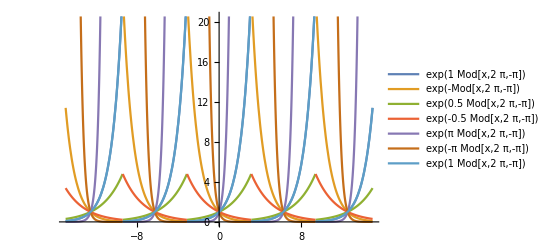

```mathematica
(*Observaremos abaixo alguns exemplos de plots para diferentes valores de λ, no primeiro gráfico veremos todos os valores plotados juntos e ao final do caderno observaremos eles em separado com sua serie de Fourier*)
Plot[{Exp[1*Mod[x,2π,-π]],Exp[-1*Mod[x,2π,-π]],Exp[0.5*Mod[x,2π,-π]], Exp[-0.5*Mod[x,2π,-π]],  Exp[π*Mod[x,2π,-π]],Exp[-π*Mod[x,2π,-π]],  Exp[1*Mod[x,2π,-π]]},{x,-15,15},PlotLegends->"Expressions"]
```

Lembrando que a série de Fourier na forma complexa é dada  pela soma: 𝒻(x)=∑_(n ∈ ℤ) c_n ℯ^(ⅈ2πnx/L)(4.1), sendo c_n= 1/L∫_0^L 𝒻(x)ℯ^(-ⅈ2πnx/L)ⅆx(4.2), para seguirmos com esse exercício devemos ter em mente que ℯ^-ⅈnx= Cos(nx)-ⅈSin(nx) (4.3).
Para  calcularmos a série de Fourier, primeiro devemos calcular o c_n:
c_n= 1/L∫_0^L 𝒻(x)ℯ^(ⅈ2πnx/L)ⅆx = 1/(2π)∫_-π^π ℯ^λx ℯ^-ⅈnx ⅆx =  1/(2π)∫_-π^π ℯ^λx[Cos(nx)-ⅈSin(nx)]ⅆx (4.4)
Separaremos a integral acima em duas partes, A = ∫_-π^π ℯ^λx Cos(nx)ⅆx e B = ∫_-π^π ℯ^λx Sin(nx)ⅆx. 
→ Resolveremos a integral A por partes, levando em consideração as seguintes informações:  Cos(θ) = Cos(-θ) ; Sin(θ) = - Sin(-θ); Sin(nπ) = 0 e Cos(nπ) = (-1)^n para n ∈ ℤ ;  Sinh = (ℯ^λπ- ℯ^-λπ)/2;∫𝒻ⅆℊ=𝒻ℊ - ∫ℊⅆ𝒻 .
∫_-π^π ℯ^λx Cos(nx)ⅆx = Cos(nx)ℯ^λx/λ|_-π^π+n/λ ∫_-π^π ℯ^λx Sin(nx)ⅆx = Cos(nx)ℯ^λx/λ|_-π^π+n/λ^2Sin(nx)ℯ^λx|_-π^π- n^2/λ^2∫_-π^π ℯ^λx Cos(nx)ⅆx
∫_-π^π ℯ^λx Cos(nx)ⅆx =  Cos(nx)ℯ^λx/λ|_-π^π+n/λ^2Sin(nx)ℯ^λx|_-π^π- n^2/λ^2∫_-π^π ℯ^λx Cos(nx)ⅆx
(1 + n^2/λ^2)∫_-π^π ℯ^λx Cos(nx)ⅆx = (1/λ^2[ℯ^λx(λCos(nx) +nSin(nx))])_-π^π =
∫_-π^π ℯ^λx Cos(nx)ⅆx = 1/(λ^2+ n^2)[ℯ^λπ(λCos(nπ) +nSin(nπ))-ℯ^-λπ(λCos(-nπ) +nSin(-nπ))]
∫_-π^π ℯ^λx Cos(nx)ⅆx = λ/(λ^2+ n^2)[ℯ^λπ(-1)^n-ℯ^-λπ (-1)^n] =  (2(λ(-1))^n)/(λ^2+ n^2)[(ℯ^λπ- ℯ^-λπ)/2] 
Portanto, A = (2(λ(-1))^n)/(λ^2+ n^2)Sinh(λπ) (4.5)
→  Resolveremos a integral  B  da mesma maneira e com as mesmas considerações:
∫_-π^π ℯ^λx Sin(nx)ⅆx = Sin(nx)ℯ^λx/λ|_-π^π-n/λ ∫_-π^π ℯ^λx Cos(nx)ⅆx = Sin(nx)ℯ^λx/λ|_-π^π-n/λ^2Cos(nx)ℯ^λx|_-π^π- n^2/λ^2∫_-π^π ℯ^λx Sin(nx)ⅆx
(1 + n^2/λ^2)∫_-π^π ℯ^λx Sin(nx)ⅆx = (1/λ^2[ℯ^λx(λSin(nx) -nCos(nx))])_-π^π =
∫_-π^π ℯ^λx Sin(nx)ⅆx = 1/(λ^2+ n^2)[ℯ^λπ(λSin(nπ) -nCos(nπ))-ℯ^-λπ(λSin(-nπ) -nCos(-nπ))]
∫_-π^π ℯ^λx Sin(nx)ⅆx = n/(λ^2+ n^2)[-ℯ^λπ(-1)^n+ℯ^-λπ (-1)^n] =  -(2(n(-1))^n)/(λ^2+ n^2)[(ℯ^λπ- ℯ^-λπ)/2] 
Portanto, B = (2(n(-1))^n)/(λ^2+ n^2)Sinh(λπ) (4.6)
Sendo c_ndado por c_n= 1/(2π)(A - ⅈB), então temos que:
c_n= 1/(2π)((2(λ(-1))^n)/(λ^2+ n^2)Sinh(λπ)- ⅈ(2(n(-1))^n)/(λ^2+ n^2)Sinh(λπ))  	⟺	c_n=((-1)^n Sinh(λπ))/(π(λ^2+ n^2)) (λ - ⅈn)
Portanto a série de Fourier da função 𝒻(x) = ℯ^λx será:
𝒻(x)= ∑_(n ∈ ℤ)^∞ ((-1)^n Sinh(λπ))/(π(λ^2+ n^2)) (λ - ⅈn)ℯ^(ⅈ2πnx/L)

	Para calcularmos os coeficientes de (𝒶_n, 𝒷_n) da formulação real, devemos levar em consideração algumas coisas vistas em aula, como:
	→ c_n^* =  c_-n= 1/2(𝒶_n + ⅈ𝒷_n)
	→ c_n= 1/2(𝒶_n- ⅈ𝒷_n)
	→ c_n+ c_n^* = 1/2(𝒶_n- ⅈ𝒷_n + 𝒶_n + ⅈ𝒷_n) = 𝒶_n  
	→ c_n- c_n^* = 1/2(𝒶_n- ⅈ𝒷_n - 𝒶_n - ⅈ𝒷_n) =-ⅈ 𝒷_n  
Com isso, seja c_n^*=((-1)^n Sinh(λπ))/(π(λ^2+ n^2)) (λ + ⅈn), temos que:
c_n+ c_n^* = ((-1)^n Sinh(λπ))/(π(λ^2+ n^2)) (λ - ⅈn +λ + ⅈn)  = 𝒶_n   	⟺		𝒶_n = 2λ((-1)^n Sinh(λ π))/(π(λ^2+ n^2))

c_n- c_n^* = ((-1)^n Sinh(λπ))/(π(λ^2+ n^2)) (λ - ⅈn-λ -ⅈn)  =- 2 ⅈ𝒷_n   	⟺		𝒷_n = -2n((-1)^n Sinh(λπ))/(π(λ^2+ n^2))

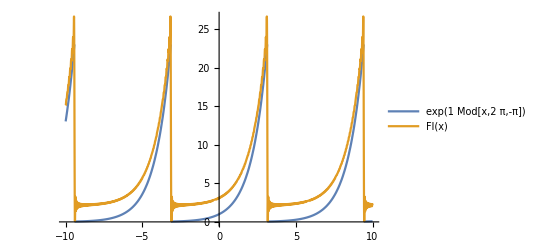

```mathematica
(*Para λ = 1*) λ = 1;
Fl[x_]:=Sinh[λ π]/(2λ)+Sum[2λ((-1)^n Sinh[λ π] Cos [n x ])/(π(λ^2+ n^2)) -2 n((-1)^n Sinh[λ π]Sin[n x])/(π(λ^2+ n^2)),{n,1,100}]
Plot[{Exp[1*Mod[x,2π,-π]],Fl[x]},{x,-10,10},PlotLegends->"Expressions"]
```

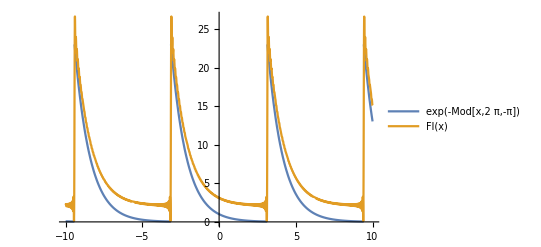

```mathematica
(*Para λ = -1*) λ = -1;
Fl[x_]:=Sinh[λ π]/(2λ)+Sum[2λ((-1)^n Sinh[λ π] Cos [n x ])/(π(λ^2+ n^2)) -2 n((-1)^n Sinh[λ π]Sin[n x])/(π(λ^2+ n^2)),{n,1,100}]
Plot[{Exp[-1*Mod[x,2π,-π]],Fl[x]},{x,-10,10},PlotLegends->"Expressions"]
```

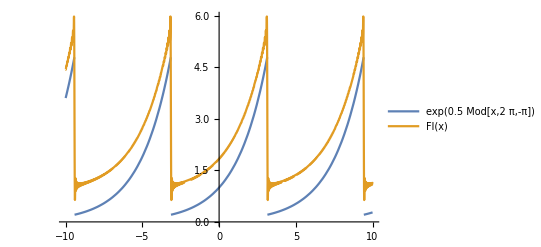

```mathematica
(*Para λ = 0.5*)λ = 0.5;
Fl[x_]:=Sinh[λ π]/(2λ)+Sum[2λ((-1)^n Sinh[λ π] Cos [n x ])/(π(λ^2+ n^2)) -2 n((-1)^n Sinh[λ π]Sin[n x])/(π(λ^2+ n^2)),{n,1,100}]
Plot[{Exp[0.5*Mod[x,2π,-π]],Fl[x]},{x,-10,10},PlotLegends->"Expressions"]
```

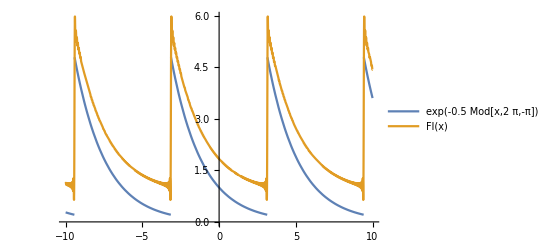

```mathematica
(*Para λ = -0.5*)λ = - 0.5;
Fl[x_]:=Sinh[λ π]/(2λ)+Sum[2λ((-1)^n Sinh[λ π] Cos [n x ])/(π(λ^2+ n^2)) -2 n((-1)^n Sinh[λ π]Sin[n x])/(π(λ^2+ n^2)),{n,1,100}]
Plot[{Exp[-0.5*Mod[x,2π,-π]],Fl[x]},{x,-10,10},PlotLegends->"Expressions"]
```

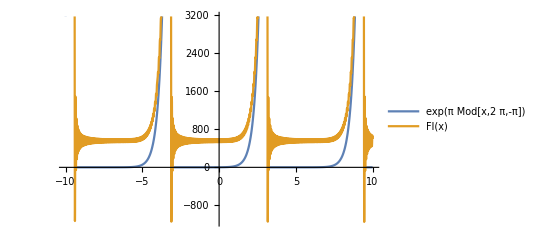

```mathematica
(*Para λ = π*)λ = π;
Fl[x_]:=Sinh[λ π]/(2λ)+Sum[2λ((-1)^n Sinh[λ π] Cos [n x ])/(π(λ^2+ n^2)) -2 n((-1)^n Sinh[λ π]Sin[n x])/(π(λ^2+ n^2)),{n,1,100}]
Plot[{Exp[π*Mod[x,2π,-π]],Fl[x]},{x,-10,10},PlotLegends->"Expressions"]
```

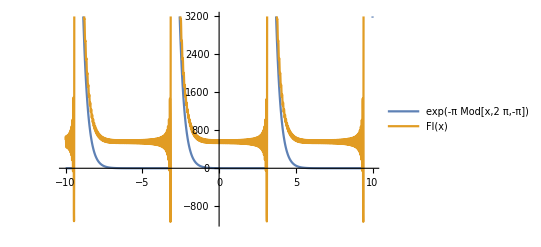

```mathematica
(*Para λ = -π*)λ =- π;
Fl[x_]:=Sinh[λ π]/(2λ)+Sum[2λ((-1)^n Sinh[λ π] Cos [n x ])/(π(λ^2+ n^2)) -2 n((-1)^n Sinh[λ π]Sin[n x])/(π(λ^2+ n^2)),{n,1,100}]
Plot[{Exp[-π*Mod[x,2π,-π]],Fl[x]},{x,-10,10},PlotLegends->"Expressions"]
```

## 5.a)

Para encontrarmos a série de Fourier ( 𝒻(x)= 𝒶_0/2+∑_(n=1)^∞ {𝒶_n Cos((2π n)/L x) + 𝒷_n Sin((2π n)/L x)}  (5.1), para os seguinte coeficientes 𝒶_0= 2/L∫_0^L 𝒻(x)ⅆx (5.2) ;	𝒶_n= 2/L∫_0^L 𝒻(x)Cos((2π n)/L x)ⅆx (5.3);	𝒷_n= 2/L∫_0^L 𝒻(x)Sin((2π n)/L x)ⅆx (5.4)) da função  𝒻(x) = Sin^2(x) para o intervalo [-π,π]. Devemos analisar primeiro a paridade da função 𝒻(x), que é uma função par (ou seja, 𝒻(x) =  𝒻(-x)), com isso nossa série de Fourier será formada por uma série de funções pares. Portanto uma série de cossenos  e, assim, 𝒷_n=0  (5.5).
Como estamos calculando a série de fourier por inspeção, não devemos calcular os coeficiente de 𝒶_0 e 𝒶_n. No entanto, podemos observar a série de Fourier da função 𝒻(x) aparecendo na seguinte relação trigonométrica: Sin^2(x) = 1/2-1/2 Cos(2x) (5.6). Essa relação trigonométrica já mostra a série de Fourier de Sin^2(x), onde 𝒶_0 = 1 (5.7) e 𝒶_2 = -1/2 (5.8), e para os demais n ≠ {0,2},  𝒶_n = 0 (5.9).

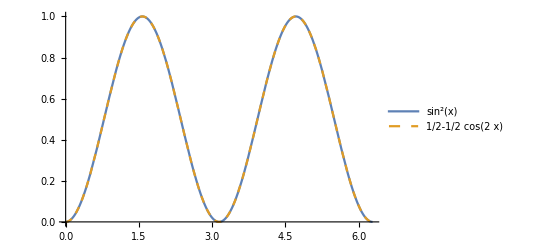

```mathematica
Plot[{(Sin[x])^2,1/2 -1/2 *Cos[2x]},{x,0,2Pi},PlotLegends->"Expressions", PlotStyle->{Thick,Dashed}]
```

## 5.b)

Nesse item resolveremos a questão de um jeito similar ao item 5.a), no entanto, usaremos a formulação complexa da série de Fourier (𝒻(x)=∑_(n ∈ ℤ) c_n ℯ^(ⅈ2πnx/L)(5.10), sendo c_n= 1/L∫_0^L 𝒻(x)ℯ^(-ⅈ2πnx/L)ⅆx(5.11)) para entendermos a série de fourier da função 𝒻(x)= ℯ^(ℯ^-ⅈx). No enunciado da questão existe uma dica, expandir a exponencial externa em série de Taylor, lembrando que série de Taylor é dada por: 𝒻(x) = ∑_(n=0)^∞ (𝒻^(n)(x_0))/(n!)(x-x_0)^n (5.12).
A expansão da função exponencial  centrada em 0 é uma das expansões mais simples e praticamente todos alunos acabam decorando ela no curso de cálculo 1, então não mostrarei os cálculos para chegar nela. 
ℯ^α =  1 + α + α^2/2+ α^3/(3!)+ α^4/(4!)+ ... (5.13)	⟺	ℯ^α =  ∑_(n=o)^∞ α^n/(n!) (5.14)
Ao substituirmos a Eq. (5.14) por α = -ⅈx, chegamos na série:
ℯ^-ⅈx =  1 + ℯ^-ⅈx + ℯ^(-2ⅈx)/2+ ℯ^(-3ⅈx)/(3!)+ ℯ^(-4ⅈx)/(4!)+ ... (5.15)	⟺	ℯ^α =  ∑_(n=o)^∞ ℯ^-nⅈx/(n!) (5.16)
O interessante dessa serie é que ao utilizarmos o comando FourierSeries[Exp[Exp[-ⅈ*x]],x,4], que nos fornece a série de Fourier pela formulação complexa, observamos que é a mesma série. Sendo então a série de Fourier da função  𝒻(x)= ℯ^(ℯ^-ⅈx):
𝒻(x)=  ℯ^(ℯ^-ⅈx) =  ∑_(n=o)^∞ ℯ^-nⅈx/(n!), sendo c_n= 1/(n!), para n ∈ ℕ.

## 6.

Para mostrarmos que sendo 𝒻 e ℊ duas funções periódicas de mesmo período L, com os coeficientes complexos de Fourier c_n e d_n: 1/L∫_0^L 𝒻^*(x)ℊ(x)ⅆx = ∑_(n ∈ ℤ) c_n^*d_n (6.1). Primeiro devemos levar em consideração que, sendo 𝒻(x)=∑_(n ∈ ℤ) c_n ℯ^(ⅈ2πnx/L)(6.2), o conjugado dela, será: 𝒻^*(x)=∑_(n ∈ ℤ) c_n^*ℯ^(-ⅈ2πnx/L)(6.3) . Além disso iremos considerar ℊ(x) como sendo ℊ(x)=∑_(n ∈ ℤ) d_n ℯ^(ⅈ2πnx/L)(6.4).  Agora, supondo a convergência das funções faremos:
𝒻^*(x)ℊ(x)=∑_(n ∈ ℤ) c_n^*ℯ^(-ⅈ2πnx/L) *∑_(n ∈ ℤ) d_n ℯ^(ⅈ2πnx/L) = ∑_(n ∈ ℤ) c_n^*d_n ℯ^(-ⅈ2πnx/L +ⅈ2πnx/L)
∫_0^L 𝒻^*(x)ℊ(x)ⅆx = ∫_0^L ∑_(n ∈ ℤ) c_n^*d_n ⅆx = L∑_(n ∈ ℤ) c_n^*d_n
 1/L∫_0^L 𝒻^*(x)ℊ(x)ⅆx = ∑_(n ∈ ℤ) c_n^*d_n (6.5)

## 7.

Sendo 𝒻(x) uma função periódica de período L = 2π no intervalo [-π, π]. A função 𝒻(x) pode ser aproximada pela serie discreta:  𝒻_N(x) = 𝒶_0 + ∑_(n=1)^N [𝒶_n Cos(nx) + 𝒷_n Sin(nx)] (7.1), sendo (𝒶_n,  𝒷_n) os coeficientes. Para escolhermos a melhor aproximação da função. Faremos a partir da função erro quadrático médio. E_N= 1/2∫_-π^π [𝒻(x) - 𝒻_N (x) ]^2 ⅆx (7.2), que após substituirmos  𝒻_N(x) ficará:   E_N= 1/2∫_-π^π [𝒻(x) -  𝒶_0 - ∑_(n=1)^N [𝒶_n Cos(nx) + 𝒷_n Sin(nx)] ]^2 ⅆx (7.3)
Para encontrarmos o valor mínimo de (𝒶_n,  𝒷_n), derivaremos a função erro quadrático por 𝒶_n e  𝒷_n, e igualaremos a zero a função, encontrando o ponto crítico da função erro que assumiremos como o nosso ponto de mínimo.
Antes de começarmos os cálculos é interessante citar algumas coisas que nos economizaram muito tempo. Como as integrais abaixo, que são frutos da ortogonalidade das funções trigonométricas.
	→Sendo δ_(n,m)= {0 para n≠m, 1 para n=m} , temos:
		→ (∫_0^L)_ Sin((2π n)/L x) Cos((2π m)/L x)ⅆx = 0 (7.4)
		→2/L(∫_0^L)_ Cos((2π n)/L x) Cos((2π m)/L x)ⅆx = δ_(n,m) (7.5)
		→ 2/L(∫_0^L)_ Sin((2π n)/L x) Sin((2π m)/L x)ⅆx = δ_(n,m) (7.6)
	→ Também vamos levar em consideração as integrais abaixo:
		→ ∫_-π^π  Cos(nx)ⅆx = (Sin(nx))/n|_-π^π= (Sin(πn) - Sin(-πn))/n = 0 (7.7)
		→ ∫_-π^π  Sin(nx)ⅆx = (Cos(nx))/n|_-π^π =  (Cos(nπ) - Cos(-πn))/n = 0 (7.8)
→ Começaremos encontrando 𝒶_n, derivaremos a Eq.  por 𝒶_n e igualando essa função por zero. Reagruparemos a função de uma maneira conveniente e resolveremos suas integrais com base na ortogonalidade das funções trigonométricas e na integral de seno e cosseno citada acima. Por fim, isolaremos 𝒶_ne chegaremos no resultado desejado.
(∂E_N)/(∂𝒶_n)= - 2 1/2∫_-π^π [𝒻(x) -  𝒶_0 - ∑_(n=1)^N [𝒶_n Cos(nx) + 𝒷_n Sin(nx)] ][ ∑_(n=1)^N Cos(nx) ]ⅆx= 0 (7.9)
∑_(n=1)^N ∫_-π^π 𝒻(x) Cos(nx)ⅆx = ∑_(n=1)^N 𝒶_0∫_-π^π  Cos(nx)ⅆx + ∑_(n=1)^N ∫_-π^π 𝒶_n  Cos^2(nx)ⅆx +  ∑_(n=1)^N (∫_-π^π)_ 𝒷_n Sin(nx) Cos(nx)ⅆx    (7.10)
∫_-π^π 𝒻(x) Cos(nx)ⅆx =  L/2 𝒶_n	 ⟺		 𝒶_n= 2/L∫_-π^π 𝒻(x) Cos(nx)ⅆx  (7.11)
→ Para encontrarmos 𝒷_n usaremos os mesmo passo a passo anterior.
(∂E_N)/(∂𝒷_n)= - 2 1/2∫_-π^π [𝒻(x) -  𝒶_0 - ∑_(n=1)^N [𝒶_n Cos(nx) + 𝒷_n Sin(nx)] ][ ∑_(n=1)^N Sin(nx) ]ⅆx= 0 (7.12)
∑_(n=1)^N ∫_-π^π 𝒻(x) Sin(nx)ⅆx = ∑_(n=1)^N 𝒶_0∫_-π^π  Sin(nx)ⅆx + ∑_(n=1)^N ∫_-π^π 𝒶_n  Sin(nx) Cos(nx)ⅆx +  ∑_(n=1)^N (∫_-π^π)_ 𝒷_n Sin^2(nx) ⅆx    (7.13) 
∫_-π^π 𝒻(x) Sin(nx)ⅆx =  L/2 𝒷_n	 ⟺		 𝒷_n= 2/L∫_-π^π 𝒻(x) Sin(nx)ⅆx  (7.14)

## 8.

Dado a função θ(x) = Piecewise[{{0, x<0}, {1, x>0}}] (8.1),  usaremos ela para definir a função  Boxcar  𝒻(x) =θ(x - u )θ(x - v) (8.2),  que também pode ser vista como 𝒻(x) = Piecewise[{{1, x ∈[u,v]}, {0, x<u e x>v}}] (8.3), onde temos a seguinte relação: -π ⩽ u ⩽ v ⩽ π (8.4). Calcularemos a série de Fourier da função Boxcar por partes em [-π,π], para u e v valores arbitrários respeitando a relação acima. Para isso, teremos:
𝒻(x)= 𝒶_0/2+∑_(n=1)^∞ {𝒶_n Cos(nx) + 𝒷_n Sin(nx)}  (8.5), para os seguinte coeficientes 𝒶_0= 1/π∫_-π^π 𝒻(x)ⅆx (8.6) ;	𝒶_n= 1/π∫_-π^π 𝒻(x)Cos(nx)ⅆx (8.7);	𝒷_n= 1/π∫_-π^π 𝒻(x)Sin(nx)ⅆx (8.8)
→Começaremos por 𝒶_0:
𝒶_0= 1/π∫_-π^π 𝒻(x)ⅆx = 1/π[∫_-π^u 𝒻(x)ⅆx + ∫_u^v 𝒻(x)ⅆx +∫_v^π 𝒻(x)ⅆx ] =  1/π∫_u^v ⅆx  
Assim, 𝒶_0=  (v-u)/π (8.9)
→ Calculo do 𝒶_n:
𝒶_n= 1/π∫_-π^π 𝒻(x)Cos(nx)ⅆx = 1/π[∫_-π^u 𝒻(x)Cos(nx)ⅆx + ∫_u^v 𝒻(x)Cos(nx)ⅆx +∫_v^π 𝒻(x)Cos(nx)ⅆx ]= 1/π ∫_u^v Cos(nx)ⅆx = 1/nπ Sin(nx)|_u^v 
Assim, 𝒶_n= 1/nπ [Sin(nv)-Sin(nu)] (8.10)
→ Calculo do 𝒷_n:
𝒷_n= 1/π∫_-π^π 𝒻(x)Sin(nx)ⅆx = 1/π[∫_-π^u 𝒻(x)Sin(nx)ⅆx + ∫_u^v 𝒻(x)Sin(nx)ⅆx +∫_v^π 𝒻(x)Sin(nx)ⅆx ]= 1/(π(v-u)) ∫_u^v Sin(nx)ⅆx = -1/(nπ(v-u)) Cos(nx)|_u^v 
Assim, 𝒷_n= -1/nπ [Cos(nv)-Cos(nu)]  (8.11)
Com isso teremos que a representação da série de Fourier real, será:
𝒻(x)=  1/(2π)+∑_(n=1)^∞ { 1/nπ [Sin(nv)-Sin(nu)] Cos(nx) -1/nπ [Cos(nv)-Cos(nu)]Sin(nx)} (8.12)
Para a representação complexa  da série de Fourier [ 𝒻(x)=∑_(n ∈ ℤ) c_n ℯ^ⅈnx (8.13)]devemos levar em consideração as relações vista em sala: c_n= 1/2(𝒶_n - ⅈ𝒷_n) (8.14), ℯ^ⅈθ= Cosθ + ⅈSinθ (8.15) , ℯ^-ⅈθ= Cosθ - ⅈSinθ (8.16), com isso c_nserá:
c_n= 1/(2nπ(v-u))[Sin(nv)-Sin(nu) + ⅈCos(nv)-ⅈCos(nu)] =  1/(2nπⅈ)[ⅈSin(nv)-ⅈSin(nu) -Cos(nv)+Cos(nu)] =  1/(2nπⅈ)[-ℯ^-ⅈvn + ℯ^-ⅈun] (8.17)
Assim, c_n=  ⅈ/(2nπ)[ℯ^-ⅈvn -ℯ^-ⅈun] (8.18) e nossa série de Fourier será: 𝒻(x)=∑_(n ∈ ℤ) ⅈ/(2nπ)[ℯ^-ⅈvn -ℯ^-ⅈun]ℯ^ⅈnx(8.19)
Abaixo, veremos alguns exemplos de série de fourier:

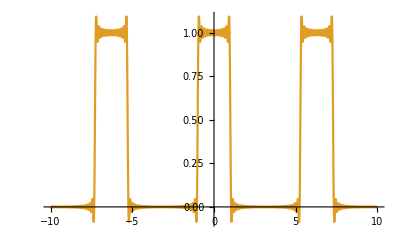

```mathematica
(*Sendo u = -1 e v = 1*) u = -1 ;v = 1;
f[x_] := Piecewise[{{1, u<x<v},{0, x< u & x>v}}];
g [x_]:= (v-u)/(2π) + Sum [(Sin[n *v]-Sin[u* n])/(n π) *Cos[n* x]- (Cos[n* v]-Cos[u* n])/(n π)*Sin[n *x],{n, 1,40}] ;
Plot[{F[Mod[x, 2π, u]],g[x] }, {x, -10, 10}, Exclusions->None]
```

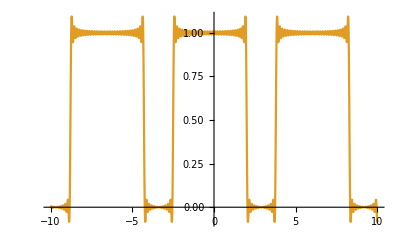

```mathematica
(*Sendo u = -2.5 e v = 2*) u = -2.5 ;v = 2;
f[x_] := Piecewise[{{1, u<x<v},{0, x< u & x>v}}];
g [x_]:= (v-u)/(2π) + Sum [(Sin[n *v]-Sin[u* n])/(n π) *Cos[n* x]- (Cos[n* v]-Cos[u* n])/(n π)*Sin[n *x],{n, 1,40}] ;
Plot[{F[Mod[x, 2π, u]],g[x] }, {x, -10, 10}, Exclusions->None]
```

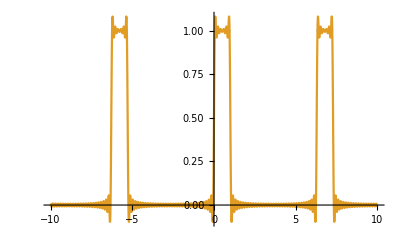

```mathematica
(*Sendo u = 0 e v = 1*) u = 0 ;v = 1;
f[x_] := Piecewise[{{1, u<x<v},{0, x< u & x>v}}];
g [x_]:= (v-u)/(2π) + Sum [(Sin[n *v]-Sin[u* n])/(n π) *Cos[n* x]- (Cos[n* v]-Cos[u* n])/(n π)*Sin[n *x],{n, 1,40}] ;
Plot[{F[Mod[x, 2π, u]],g[x] }, {x, -10, 10}, Exclusions->None]
```

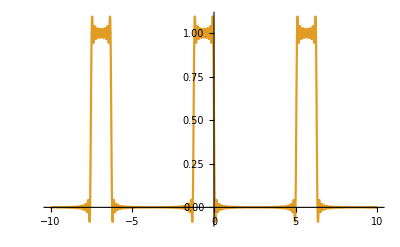

```mathematica
(*Sendo u = -1.25 e v = 0*) u = -1.25 ;v = 0;
f[x_] := Piecewise[{{1, u<x<v},{0, x< u & x>v}}];
g [x_]:= (v-u)/(2π) + Sum [(Sin[n *v]-Sin[u* n])/(n π) *Cos[n* x]- (Cos[n* v]-Cos[u* n])/(n π)*Sin[n *x],{n, 1,40}] ;
Plot[{F[Mod[x, 2π, u]],g[x] }, {x, -10, 10}, Exclusions->None]
```

Se o nosso vagão for simétrico, ou seja, u=-v, teremos então uma função par e com isso o nosso 𝒷_n=0. Podemos observar isso analisando os coeficientes:
 𝒶_0=  (v-u)/π= (2v)/π
 𝒶_n= 1/nπ [Sin(nv)-Sin(-nv)] = 2/nπ Sin(nv)
 𝒷_n= -1/nπ [Cos(nv)-Cos(-nv)] = 0

## 9.

Do exercício anterior tiro que a função Boxcar é representada por 𝒻(x) =θ(x - u )θ(x - v)(9.1)  e que a sua série de Fourier é dada por 𝒻(x)=∑_(n ∈ ℤ) ⅈ/(2nπ)[ℯ^-ⅈvn -ℯ^-ⅈun]ℯ^ⅈnx(9.2)
Para o nosso exercício teremos que u = b - a (9.3)e v = b + a (9.4). Com isso, então:
𝒻(x) =θ(x -  b + a )θ(x - b - a) = ∑_(n ∈ ℤ) ⅈ/(2nπ)[ℯ^(-ⅈ(b+a)n) -ℯ^(-ⅈ(b-a)n)]ℯ^ⅈnx= ∑_(n ∈ ℤ) (- ⅈⅈ)/(2nπⅈ)[-ℯ^-ⅈan +ℯ^ⅈan]ℯ^ⅈnx ℯ^-ⅈbn = ∑_(n ∈ ℤ) 1/nπ Sin[na]ℯ^ⅈnx ℯ^-ⅈbn (9.5).
Adaptando a função delta de Dirac que vimos nas notas de aula para o nosso caso, temos:
δ(x) = a→^Lim 0(θ(x-b+a)θ(x-b-a))/(2a)= a→^Lim 0 ∑_(n ∈ ℤ) 1/nπ Sin[na]/(2a)ℯ^ⅈnx ℯ^-ⅈbn = ∑_(n ∈ ℤ) (ℯ^ⅈnx ℯ^-ⅈbn)/(2π)a→^Lim 0 Sin[na]/an, pelo limite fundamental do calculo temos por fim:
δ(x) =  ∑_(n ∈ ℤ) (ℯ^ⅈnx ℯ^-ⅈbn)/(2π)(9.6)